(-2 | 5
1 | 3
2 | -1
3 | 0
4 | 1
5 | 9
6 | 0
7 | 2
8 | 6
-1 | -4)

{-42+20 {0.336601,0.489314,-0.408443,0.0348495}[0]+66 {0.336601,0.489314,-0.408443,0.0348495}[1]+418 {0.336601,0.489314,-0.408443,0.0348495}[2]+2574 {0.336601,0.489314,-0.408443,0.0348495}[3],-212+66 {0.336601,0.489314,-0.408443,0.0348495}[0]+418 {0.336601,0.489314,-0.408443,0.0348495}[1]+2574 {0.336601,0.489314,-0.408443,0.0348495}[2]+17578 {0.336601,0.489314,-0.408443,0.0348495}[3],2 (-738+209 {0.336601,0.489314,-0.408443,0.0348495}[0]+1287 {0.336601,0.489314,-0.408443,0.0348495}[1]+8789 {0.336601,0.489314,-0.408443,0.0348495}[2]+61743 {0.336601,0.489314,-0.408443,0.0348495}[3]),22 (-446+117 {0.336601,0.489314,-0.408443,0.0348495}[0]+799 {0.336601,0.489314,-0.408443,0.0348495}[1]+5613 {0.336601,0.489314,-0.408443,0.0348495}[2]+40639 {0.336601,0.489314,-0.408443,0.0348495}[3])}

(20 | 66 | 418 | 2574
66 | 418 | 2574 | 17578
418 | 2574 | 17578 | 123486
2574 | 17578 | 123486 | 894058)

-42

-212

-1476

-9812

{0.336601,0.489314,-0.408443,0.0348495}

0.336601+0.489314 x-0.408443 x^2+0.0348495 x^3

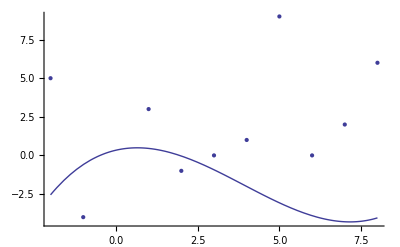

```mathematica
m=10;
n=4;
XY={{-2,5},{1,3},{2,-1},{3,0},{4,1},{5,9},{6,0},{7,2},{8,6},{-1,-4}};
B=Table[Table[0,{i,1,n}],{j,1,n}];
MatrixForm[XY]
p[x_]=a[0]+a[1] x+a[2] x^2+a[3] x^3;
S=Sum[(XY[[i,2]]-p[XY[[i,1]]])^2,{i,1,m}];
A=Table[FullSimplify[D[S,a[i]]],{i,0,3}]
Do[
B[[i]]=Coefficient[A[[i]],Table[a[j],{j,0,3}]]
,{i,1,n}]
MatrixForm[B]
Do[
h[i]=FullSimplify[A[[i]]-Sum[B[[i,j]]*a[j-1],{j,1,4}]];Print[h[i]],{i,1,4}]
b=Table[h[i],{i,1,4}];
a=N[LinearSolve[B,b]]
App[x_]=a[[1]]+a[[2]] x+a[[3]] x^2+a[[4]] x^3
R1=ListPlot[XY];
R2=Plot[App[x],{x,-2,8}];
Show[R1,R2]
```